```mathematica
RecurFact[n_]:= If[n<0, Return["error"], If[n==0, 1, If[n==1, 1, Return[n*RecurFact[n-1]]]]]
RecurFact[5]
```

120

-Graphics3D-

-Graphics3D-

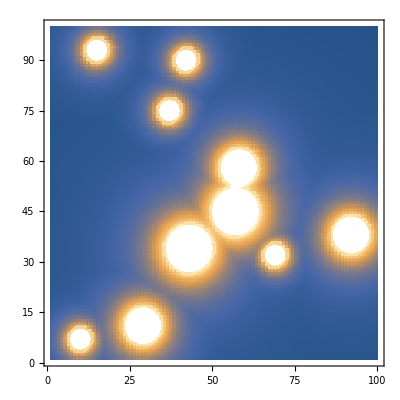

38144446

93510850

```mathematica
(*Initial values*)
Size = 100;
towersTable = Table[0, {i, 1, Size}, {j , 1,Size}];
(*peopleTable = RandomInteger[{1, 10000}, {Size, Size}];*)
peopleTable =Table[0, {i, 1, Size}, {j , 1,Size}];
towersCordinates=RandomInteger[{1, Size}, {10, 2}];

For[i = 1, i<Size+1,
For[j=1, j<Size+1,
If[i+j>=Size+1,peopleTable[[i, j]]=(i+j)^2];
j++];
i++]

ListPlot3D[peopleTable]
(*Place towers*)
For[i=1, i< 6, towersTable[[towersCordinates[[i, 1]], towersCordinates[[i, 2]]]] = 100;i++];
For[i=6, i< 10, towersTable[[towersCordinates[[i, 1]], towersCordinates[[i, 2]]]] = 300;i++];
For[i=9, i< 11, towersTable[[towersCordinates[[i, 1]], towersCordinates[[i, 2]]]] = 500;i++];

(*Find powers*)
For[i = 1, i < Size+1,i++,
For[j=1, j < Size+1,j++,
If[towersTable[[i, j]]≠0, Continue[]];
P1 = 100/(((i-towersCordinates[[1, 1]])^2) + ((j-towersCordinates[[1, 2]])^2));
P2 = 100/(((i-towersCordinates[[2, 1]])^2) + ((j-towersCordinates[[2, 2]])^2));
P3 = 100/(((i-towersCordinates[[3, 1]])^2) + ((j-towersCordinates[[3, 2]])^2));
P4 = 100/(((i-towersCordinates[[4, 1]])^2) + ((j-towersCordinates[[4, 2]])^2));
P5 = 100/(((i-towersCordinates[[5, 1]])^2) + ((j-towersCordinates[[5, 2]])^2));
P6 = 300/(((i-towersCordinates[[6, 1]])^2) + ((j-towersCordinates[[6, 2]])^2));
P7 = 300/(((i-towersCordinates[[7, 1]])^2) + ((j-towersCordinates[[7, 2]])^2));
P8 = 300/(((i-towersCordinates[[8, 1]])^2) + ((j-towersCordinates[[8, 2]])^2));
P9 = 500/(((i-towersCordinates[[9, 1]])^2) + ((j-towersCordinates[[9, 2]])^2));
P10 = 500/(((i-towersCordinates[[10, 1]])^2) + ((j-towersCordinates[[10, 2]])^2));
towersTable[[i, j]] = Max[P1, P2, P3, P4, P5, P6, P7, P8, P9, P10];
]
]

(*How many people*)
goodConnection = 0;
n=0;
For[i = 1, i<Size+1,
For[j=1, j<Size+1,
n+=peopleTable[[i, j]];
If[towersTable[[i, j]]>1, goodConnection+=peopleTable[[i, j]]];
;j++]
;i++]

ListPlot3D[towersTable, PlotRange->All]
ListDensityPlot[towersTable]
goodConnection
n
```

```mathematica
(*Initial values*)
Size = 15;
field = Table[0, {i, 1, Size}, {j, 1, Size}];
visited = Table[0, {i, 1, Size}, {j, 1, Size}];
start ={0, 0};
isOut=0;

field[[3, 2]] = 1; field[[3, 13]] = 1; field[[5, 13]] = 1; field[[5, 15]] = 1 ;field[[10, 15]] = 1 ;field[[10, 2]] = 1;n=6;

(*Find start*)
For[i = Size, i > 0, i--,
For[j = 1, j < Size+1, j++,
If[field[[i, j]]==1, start={i, j}; isOut=1;Break[]];
]
If[isOut==1, Break[]];
]

visited[[start[[1]], start[[2]]]]=1;

current = start

isContinue = 0;
counter = 0;

(*Find a way*)
While[counter≠n-1, 

isContinue=0;
For[j =current[[2]]+1, j<Size+1, j++,
If[field[[current[[1]], j]]==1 && visited[[current[[1]], j]]≠1, current={current[[1]], j}; visited[[current[[1]], j]] = 1;Print[current];isContinue=1; counter++;Break[]];
];
If[isContinue==1, Continue[];];

isContinue=0;
For[i = current[[1]]-1, i>0, i--,
If[field[[i, current[[2]]]]==1 && visited[[i, current[[2]]]]≠1, current={i, current[[2]]};visited[[i, current[[2]]]]=1;Print[current];isContinue=1;counter++;Break[]];
];
If[isContinue==1, Continue[];];

isContinue=0;
For[j =current[[2]]-1, j>0, j--,
If[field[[current[[1]], j]]==1 && visited[[current[[1]], j]]≠1, current={current[[1]], j}; visited[[current[[1]], j]] = 1;Print[current];isContinue=1; counter++;;Break[]];
];
If[isContinue==1, Continue[];];


isContinue=0;
For[i = current[[1]]+1, i<Size+1, i++,
If[field[[i, current[[2]]]]==1 && visited[[i, current[[2]]]]≠1, current={i, current[[2]]};visited[[i, current[[2]]]]=1;Print[current];isContinue=1;counter++;Break[]];
];
If[isContinue==1, Continue[];];

]
Print[start];
```

{10,2}

{10,15}

{5,15}

{5,13}

{3,13}

{3,2}

{10,2}